```mathematica
0,0,0
1,0,1
2,1,0
3,1,1
```

```mathematica
tf[x_]:=Piecewise[{{Piecewise[{{1, TrueQ[x]}, {0, ¬TrueQ[x]}}], BooleanQ[x]}, {0, ¬BooleanQ[x]}}]
```

```mathematica
ntoval[{x_,y_}]:=2x+y
nffromval[z_]:={Expand[InterpolatingPolynomial[{{0,0},{1,0},{2,1},{3,1}},z]],Expand[InterpolatingPolynomial[{{0,0},{1,1},{2,0},{3,1}},z]]}
nf[x_,y_]:=InterpolatingPolynomial[{{{0,0},1},{{0,1},1},{{1,0},1},{{1,1},0}},{x,y}]
nf[z_]:=Expand[InterpolatingPolynomial[{{0,1},{1,1},{2,1},{3,0}},z]]
nffromval[z]
nf[x,y]
nf[z]
```

{-(7 z)/6+(3 z^2)/2-z^3/3,(10 z)/3-3 z^2+(2 z^3)/3}

1-x y

1-z/3+z^2/2-z^3/6

```mathematica
base=17;
ntoval[{x_,y_}]:=2x+y
nfromval[z_]:={PolyModReduce[InterpolatingPolynomial[{{0,0},{1,0},{2,1},{3,1}},z],base],PolyModReduce[InterpolatingPolynomial[{{0,0},{1,1},{2,0},{3,1}},z],base]}
nd0[x_,y_]:=PolyModReduce[InterpolatingPolynomial[{{{0,0},1},{{0,1},1},{{1,0},1},{{1,1},0}},{x,y}],base]
nd[x0_,y0_]:=Block[{x=PolyModReduce[x0,base],y=PolyModReduce[y0,base]},nd0[x,y]]
nd[z_]:=PolyModReduce[InterpolatingPolynomial[{{0,1},{1,base+1},{2,2base+1},{3,3base}},z],base]
nfromval[z]
nd0[x,y]
nd[x,y]
nd[z]
```

{z+2 z^2+3 z^3,z+2 z^2}

1

1

1+3 z+z^2+2 z^3

```mathematica
17*3
```

51

```mathematica
PolynomialMod[Expand[InterpolatingPolynomial[{{{0,0},1},{{0,1},18},{{1,0},35},{{1,1},51}},{x,y}]],17]
```

```mathematica
nd[x_,y_]:=1+16 x y
```

```mathematica
{0,0,0,0,1,1,1,1}
```

```mathematica
xs={1,2,3,...,2^n-1}
ys={1,1,1,1,0,0,0,0}
```

```mathematica
(∏_(m=0)^(j-1) 1/(j-m))(∏_(m=j+1)^k 1/(j-m))(∏_(m=0)^k (x-m)/(x-j))
```

```mathematica
∑_(j=1)^(2^(n-1)) ((-1)^(2+k) (j-x)^(-1-k) x Pochhammer[1-x,k])/(j Gamma[1-j+k] Pochhammer[1-j,-1+j])
```

0

```mathematica
Expand[InterpolatingPolynomial[{{0,0},{1,1},{2,0},{3,1}},x]]
```

(10 x)/3-3 x^2+(2 x^3)/3

```mathematica
First[Last[FactorInteger[24354]]]
```

41

```mathematica
Monitor[Table[Max[Table[Max[Map[First[Last[FactorInteger[Denominator[#]]]]&,CoefficientList[Expand[InterpolatingPolynomial[Table[{i,PadLeft[IntegerDigits[i,2],k][[j]]},{i,0,2^k-1}],x]],x]]],{j,1,k}]],{k,2,10}],{k,j,i}]
```

{3,7,13,31,61,127,251,509,1021}

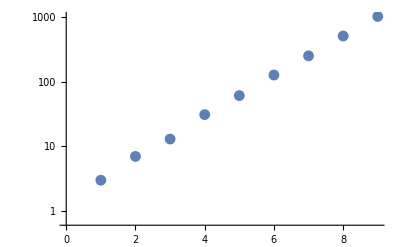

```mathematica
ListLogPlot[{3,7,13,31,61,127,251,509,1021}]
```

```mathematica
Table[PolyModReduce[Expand[InterpolatingPolynomial[Table[{i,PadLeft[IntegerDigits[i,2],4][[j]]},{i,0,2^4-1}],x]],base],{j,1,4}]
Table[FactorInteger[Denominator[Factor[Expand[InterpolatingPolynomial[Table[{i,PadLeft[IntegerDigits[i,2],4][[j]]},{i,0,2^4-1}],x]]]]],{j,1,4}]
```

{x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15,16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15,9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15}

{{{2,9},{3,5},{5,3},{7,2},{11,1},{13,1}},{{2,8},{3,6},{5,3},{7,2},{11,1},{13,1}},{{2,5},{3,6},{5,3},{7,2},{11,1},{13,1}},{{3,6},{5,3},{7,2},{11,1},{13,1}}}

```mathematica
FactorInteger[120120]
```

{{2,3},{3,1},{5,1},{7,1},{11,1},{13,1}}

```mathematica
nd1[x_,y_]:=1+2 x+y+3 x y
```

```mathematica
n4toval[{x_,y_}]:=2x+y
n4fromval[z_]:={z/6-z^2/2+z^3/3,z^2}
n4[{x_,y_}]:=1-(2 x)/3+2 x^2-(4 x^3)/3-y/3+2 x y-2 x^2 y+y^2/2-x y^2-y^3/6(*1-(2x+y)/3+(2x+y)^2/2-(2x+y)^3/6*)
n4[x_,y_]:=1-(2 x)/3+2 x^2-(4 x^3)/3-y/3+2 x y-2 x^2 y+y^2/2-x y^2-y^3/6(*1-(2x+y)/3+(2x+y)^2/2-(2x+y)^3/6*)
n4[z_]:=1-x/3+x^2/2-x^3/6
{Table[n4toval[{x,y}],{x,0,1},{y,0,1}]//TableForm,Table[Mod[n4fromval[z],4],{z,0,3}],Table[n4[{x,y}],{x,0,1},{y,0,1}]//TableForm}
```

{0 | 1
2 | 3,{{0,0},{0,1},{1,0},{1,1}},1 | 1
1 | 0}

```mathematica
Mod[Expand[n4[n4toval[{n4[a],n4[a]}]]],4]
```

Mod[1-x/3+x^2/2-x^3/6,4]

```mathematica
BooleanMinimize[x⊼x]
```

!x

```mathematica
BooleanConvert[(a∨b)∧(¬b∨c),"NAND"]
```

(a⊼!b)⊼(b⊼c)

```mathematica
(a⊼(b⊼b))⊼(b⊼c)
(a⊼(n4[b,b]))⊼n4[b,c]
bigpoly=Expand[n4[(n4[a,(n4[b,b])]),n4[b,c]]];
```

(a⊼(b⊼b))⊼(b⊼c)

(a⊼1-b+(9 b^2)/2-(9 b^3)/2)⊼1-(2 b)/3+2 b^2-(4 b^3)/3-c/3+2 b c-2 b^2 c+c^2/2-b c^2-c^3/6

```mathematica
bigpoly5=PolyModReduce[Expand[nd[(nd[a,(nd[b,b])]),nd[b,c]]],5]-1
```

```mathematica
BooleanMinimize[(x1 ∨ x2) ∧ (x2 ∨ x3) ∧ (x3 ∨ x4) ∧ ( ¬x1 ∨ ¬x3) ∧ (¬x2 ∨ ¬x4)]
```

!x1&&x2&&x3&&!x4

```mathematica
BooleanConvert[(x1 ∨ x2) ∧ (x2 ∨ x3) ∧ (x3 ∨ x4) ∧ ( ¬x1 ∨ ¬x3) ∧ (¬x2 ∨ ¬x4),"NAND"]
```

```mathematica
!((!x1⊼x2)⊼x3)⊼(!x4))
!((nd[nd[x1,x1],x2])⊼x3)⊼(nd[x4,x4])
nd[nd[nd[nd[nd[x1,x1],x2],x3],nd[x4,x4]],nd[nd[nd[nd[x1,x1],x2],x3],nd[x4,x4]]]
nd[nd[nd[nd[nd[x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15,x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15],16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15],9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15],nd[13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15]],nd[nd[nd[nd[x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15,x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15],16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15],9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15],nd[13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15]]]
```

```mathematica
PolynomialMod[Expand[nd[nd[nd[nd[nd[x1,x1],x2],x3],nd[x4,x4]],nd[nd[nd[nd[x1,x1],x2],x3],nd[x4,x4]]]],5]
```

4 x3+4 x2 x3+4 x1^2 x2 x3+x3^2+2 x2 x3^2+2 x1^2 x2 x3^2+x2^2 x3^2+2 x1^2 x2^2 x3^2+x1^4 x2^2 x3^2+4 x4^2+x3 x4^2+x2 x3 x4^2+x1^2 x2 x3 x4^2+2 x3^2 x4^2+4 x2 x3^2 x4^2+4 x1^2 x2 x3^2 x4^2+2 x2^2 x3^2 x4^2+4 x1^2 x2^2 x3^2 x4^2+2 x1^4 x2^2 x3^2 x4^2+x4^4+2 x3 x4^4+2 x2 x3 x4^4+2 x1^2 x2 x3 x4^4+x3^2 x4^4+2 x2 x3^2 x4^4+2 x1^2 x2 x3^2 x4^4+x2^2 x3^2 x4^4+2 x1^2 x2^2 x3^2 x4^4+x1^4 x2^2 x3^2 x4^4

```mathematica
{x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15,16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15,9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15}//Column
```

x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15
16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15
9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15
13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15

```mathematica
nd1[nd1[nd1[nd1[x1,x1],x2],x3],nd1[x4,x4]]
```

```mathematica
bigpoly52=nd1[2+2 (1+2 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2)+x3+3 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2) x3)+3 x4+3 x4^2+3 (1+2 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2)+x3+3 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2) x3) (1+3 x4+3 x4^2),2+2 (1+2 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2)+x3+3 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2) x3)+3 x4+3 x4^2+3 (1+2 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2)+x3+3 (1+2 (1+3 x1+3 x1^2)+x2+3 (1+3 x1+3 x1^2) x2) x3) (1+3 x4+3 x4^2)];
```

```mathematica
Sort[DeleteDuplicates[Flatten[CoefficientList[bigpoly52-1,{x1,x2,x3,x4}]]]]
```

{4218,4800,7500,9000,10800,11250,13068,13500,14400,14850,15552,17280,18000,21600,24300,25500,26136,27000,27918,28512,31104,32040,32400,32832,34650,34992,35640,38250,38880,40050,42768,45900,46656,48060,48600,51300,51840,54675,57024,58320,60552,64800,67050,69984,70650,71280,72900,73872,75690,77760,78732,81648,85536,86940,87480,90828,91260,93312,97200,98496,100575,103275,104976,109350,110808,116640,122472,123120,123930,136890,137700,139968,145800,147744,148716,155520,157464,163296,164700,165240,166212,172908,174960,177147,184680,194400,196830,197775,209952,215784,221616,227448,233280,234738,236196,240570,244944,253530,259362,262440,297432,313956,314928,323676,332424,334611,349920,350892,354294,360855,371790,373977,393660,419904,431568,443232,446148,454896,456354,472392,480978,495720,498636,524880,629856,638604,647352,664848,669222,684531,699840,706401,708588,710775,747954,892296,941868,944784,997272,1259712,1277208,1329696,1349379}

```mathematica
PolyModReduce[PolynomialMod[nd[13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15],17],17]
```

```mathematica
ndm[x_,y_]:=PolynomialMod[1+16 x y,17]
```

```mathematica
bigpoly5=ndm[ndm[ndm[ndm[ndm[x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15,x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15],16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15],9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15],ndm[13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15]],ndm[ndm[ndm[ndm[x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15,x+5 x^2+8 x^3+10 x^4+16 x^5+13 x^6+11 x^7+8 x^8+10 x^9+5 x^10+14 x^11+10 x^12+10 x^13+13 x^14+2 x^15],16 x+16 x^2+3 x^3+3 x^4+5 x^5+14 x^6+4 x^7+10 x^8+3 x^9+12 x^10+11 x^11+11 x^12+12 x^13+15 x^14+x^15],9 x+12 x^2+9 x^3+x^4+9 x^5+x^6+9 x^7+12 x^8+9 x^9+3 x^10+9 x^11+2 x^12+9 x^13+16 x^14+9 x^15],ndm[13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15,13 x+8 x^2+8 x^3+8 x^4+4 x^5+8 x^6+14 x^7+8 x^8+9 x^9+8 x^10+13 x^11+8 x^12+7 x^13+8 x^14+13 x^15]]];
```

```mathematica
bigpoly5
```

```mathematica
Table[Mod[1+4 x^2+14 x^3+16 x^4+9 x^5+11 x^7+4 x^8+7 x^9+14 x^10+14 x^11+6 x^12+8 x^13+11 x^14+12 x^15+4 x^16+2 x^17+9 x^18+2 x^19+14 x^21+14 x^22+10 x^23+x^24+12 x^25+11 x^27+9 x^28+12 x^29+16 x^31+7 x^32+3 x^33+11 x^34+16 x^35+15 x^36+13 x^37+8 x^38+7 x^39+14 x^41+13 x^42+x^43+6 x^44+3 x^45+2 x^46+9 x^47+10 x^48+x^49+6 x^50+10 x^51+5 x^52+12 x^53+8 x^54+4 x^55+7 x^56+13 x^57+13 x^58+13 x^59+13 x^60+x^61+3 x^62+6 x^64+x^65+9 x^66+12 x^67+9 x^68+10 x^69+x^70+12 x^71+11 x^72+2 x^73+14 x^74+2 x^75+10 x^76+9 x^77+9 x^78+10 x^79+11 x^80+7 x^81+9 x^82+12 x^83+7 x^84+14 x^85+x^86+9 x^87+8 x^88+2 x^89+15 x^90+10 x^91+10 x^93+11 x^94+2 x^95+6 x^96+4 x^97+2 x^98+10 x^99+6 x^100+4 x^101+16 x^102+15 x^103+8 x^104+7 x^105+15 x^106+15 x^107+4 x^108+12 x^109+4 x^110+7 x^111+9 x^112+9 x^113+3 x^114+7 x^115+10 x^116+5 x^117+14 x^118+8 x^119+4 x^120+12 x^121+4 x^122+2 x^123+x^124+11 x^125+11 x^126+7 x^127+16 x^128+6 x^130+8 x^132+x^134+x^135+x^136+12 x^137+12 x^138+11 x^139+9 x^140+13 x^141+4 x^142+13 x^143+9 x^144+4 x^145+15 x^146+6 x^147+4 x^148+x^149+5 x^150+8 x^151+5 x^152+16 x^153+15 x^154+16 x^155+2 x^156+9 x^157+x^158+9 x^159+13 x^160+4 x^161+13 x^162+9 x^163+16 x^164+4 x^165+5 x^166+16 x^167+9 x^168+15 x^170+11 x^171+15 x^172+3 x^173+14 x^174+14 x^175+13 x^176+2 x^177+12 x^178+11 x^179+13 x^180-1,17],{x,0,16}]
```

{0,16,16,16,0,16,0,16,0,16,16,16,0,16,16,16,9}

```mathematica
Sort[DeleteDuplicates[Flatten[CoefficientList[bigpoly5-1,{x1,x2,x3,x4}]]]]
```

{0,1,2,3}

```mathematica
bigpolyf=Expand[nf[nf[nf[nf[nf[x1,x1],x2],x3],nf[x4,x4]],nf[nf[nf[nf[x1,x1],x2],x3],nf[x4,x4]]]];
```

```mathematica
rannfcolist[numvars_,length_]:=Block[{ranpoly=Expand[ToExpression[StringJoin[Table[StringJoin["nf[x",ToString[RandomInteger[numvars]],","],{i,1,length}],StringJoin["nf[x",ToString[RandomInteger[numvars]]],Table["]",{i,1,length+1}]]]]},Sort[DeleteDuplicates[Flatten[CoefficientList[ranpoly,Variables[ranpoly]]]]]]
rannfcolist[20,30]
```

{-1,-1/3,-1/6,0,1/2,1}

```mathematica
Permute[Range[3],RandomPermutation[3]]
```

{3,1,2}

```mathematica
flexibleTake[list_,{x_,y_}]:=Block[{len=Length[list]},Piecewise[{{{list[[x]]}, (x==y)∨(x≥len)}, {Take[list,{x,y}], (x≠y)∧(x<len)∧(y≤len)}, {Take[list,{x,len}], (x≠y)∧(x<len)∧(y>len)}}]]
ranapply[list_]:=Block[{len=Length[list]},Block[{pos(*ition*)=RandomInteger[{1,len-1}]},
Join[flexibleTake[list,{1,pos-1}],Block[{apppiece=flexibleTake[list,{pos,pos+1}]},{f[apppiece[[1]],apppiece[[2]]]}],Piecewise[{{Drop[list,pos+1], pos+2<len}, {{}, pos+2≥len}}]]]]
ranapply[{a,b,c,d,e,f}]
ranapply[{a,b,c,d}]
```

{a,b,c,f[d,e]}

{f[a,b],c,d}

```mathematica
ranapplyall[list_]:=
```

```mathematica
bigpoly52=Expand[nd[nd[nd[nd[nd[x1,x1],x2],x3],nd[x4,x4]],nd[nd[nd[nd[x1,x1],x2],x3],nd[x4,x4]]]];
```

$Aborted

```mathematica
Factor[bigpoly52]
```

```mathematica
bp5[a_,b_,c_]:=Mod[-1+a+3 a b^2+b c+3 a b c+a b^3 c,5]
```

```mathematica
Table[{a,b,c,bp5[a,b,c]},{a,0,1},{b,0,1},{c,0,1}]
```

{{{{0,0,0,4},{0,0,1,4}},{{0,1,0,4},{0,1,1,0}}},{{{1,0,0,0},{1,0,1,0}},{{1,1,0,3},{1,1,1,3}}}}

```mathematica
bigpoly
```

```mathematica
Denominator[2/3]
```

3

```mathematica
MemberQ[Rationals,23]
```

False

```mathematica
MemberQ[Rationals,234]
```

False

```mathematica
LCM@@{1,2,3}
```

6

```mathematica
LCM@@Delete[Map[Abs,DeleteDuplicates[Flatten[CoefficientList[Expand[82944*bigpoly],{a,b,c}]]]],1]
```

903091563717125559892259302217208025718123789419647020541412671391288748098118681779992049059643399681902272712587832456199327506672102324304736384120082018889203519739367536214295257555273120245329781755636178822888531636859107499971022720664071061883202427303123642679296000

```mathematica
FractionalMod[r_,m_Integer]:=Piecewise[{{r, ListQ[r]}, {Mod[r,4], ((Denominator[r]==1)∨(r==0))∧(¬ListQ[r])}, {Piecewise[{{Mod[Numerator[r]PowerMod[Denominator[r],-1,m],m], GCD[Denominator[r],m]==1}, {Mod[Numerator[r],4]/Denominator[r], GCD[Denominator[r],m]≠1}}], (Denominator[r]≠1)∧(r≠0)∧(¬ListQ[r])}}]
FractionalMod[33/43,4]
```

3

```mathematica
Expand[PolyModReduce[Expand[(bigpoly-1)],4]]
```

3+(25 a)/9+(32 a^2)/9+(68 a^3)/81+(32 a^4)/9+(16 a^5)/27+(8 a^6)/9+(44 a^7)/27+(256 a^9)/81+(11 b)/6+(4 a b)/3+(8 a^2 b)/9+(4 a^3 b)/3+(4 a^4 b)/3+(4 a^5 b)/3+(8 a^6 b)/3+(16 a^8 b)/9+(7 b^2)/12+(8 a b^2)/3+(26 a^2 b^2)/9+(28 a^3 b^2)/9+(32 a^4 b^2)/9+(4 a^5 b^2)/9+(32 a^6 b^2)/9+(4 a^7 b^2)/9+(15 b^3)/4+(2 a b^3)/3+(2 a^2 b^3)/9+(20 a^4 b^3)/9+(4 a^5 b^3)/3+(8 a^6 b^3)/9+(5 b^4)/4+(5 a b^4)/2+(2 a^2 b^4)/3+(10 a^3 b^4)/3+(4 a^4 b^4)/3+(8 a^5 b^4)/3+(5 b^5)/2+(a b^5)/3+(5 a^2 b^5)/3+(8 a^3 b^5)/3+(10 a^4 b^5)/3+(73 b^6)/24+(8 a b^6)/3+(a^2 b^6)/2+(8 a^3 b^6)/3+3 a^4 b^6+(5 b^7)/8+(5 a b^7)/2+(5 a^2 b^7)/2+2 a^3 b^7+a^4 b^7+(27 b^8)/8+(19 a b^8)/16+(5 a^2 b^8)/4+(7 a^3 b^8)/4+a^4 b^8+2 a^5 b^8+(283 b^9)/96+(7 a b^9)/2+(13 a^2 b^9)/8+3 a^3 b^9+2 a^4 b^9+(227 b^10)/64+(9 a b^10)/16+(21 a^2 b^10)/16+(7 a^3 b^10)/2+(7 a^4 b^10)/2+(163 b^11)/64+(35 a b^11)/16+(23 a^2 b^11)/16+2 a^3 b^11+(a^4 b^11)/2+(27 b^12)/32+(187 a b^12)/64+(9 a^2 b^12)/8+3 a^4 b^12+2 a^5 b^12+(61 b^13)/128+(103 a b^13)/32+(7 a^2 b^13)/8+(5 a^3 b^13)/2+2 a^4 b^13+(925 b^14)/256+(197 a b^14)/64+(7 a^2 b^14)/8+(15 a^3 b^14)/4+(3 a^4 b^14)/2+(187 b^15)/256+(33 a b^15)/16+(27 a^2 b^15)/8+(a^4 b^15)/2+(881 b^16)/256+(765 a b^16)/256+(a^2 b^16)/16+(7 a^3 b^16)/4+(621 b^17)/512+3 a b^17+(23 a^2 b^17)/16+(a^3 b^17)/2+(3109 b^18)/1024+(69 a b^18)/32+(39 a^2 b^18)/16+(5 a^3 b^18)/4+(3723 b^19)/1024+(87 a b^19)/32+(61 a^2 b^19)/16+(37 b^20)/32+(171 a b^20)/128+(23 a^2 b^20)/16+(991 b^21)/256+(3 a b^21)/32+(15 a^2 b^21)/16+(503 b^22)/512+(19 a b^22)/64+(1141 b^23)/512+(7 a b^23)/32+(721 b^24)/256+(889 a b^24)/256+(1541 b^25)/512+(1857 b^26)/1024+(1159 b^27)/1024+(11 c)/18+(4 a c)/9+(2 a^2 c)/27+(20 a^3 c)/9+(92 a^4 c)/27+(32 a^6 c)/27+(11 b c)/3+(10 a b c)/9+20/9 a^2 b c+4/9 a^3 b c+32/9 a^4 b c+4/9 a^5 b c+8/9 a^6 b c+(13 b^2 c)/6+31/9 a b^2 c+8/3 a^2 b^2 c+32/9 a^3 b^2 c+8/9 a^4 b^2 c+4/3 a^5 b^2 c+28/9 a^6 b^2 c+(13 b^3 c)/6+19/9 a b^3 c+4/3 a^2 b^3 c+8/9 a^3 b^3 c+4/3 a^4 b^3 c+8/3 a^5 b^3 c+(31 b^4 c)/8+11/3 a b^4 c+8/3 a^2 b^4 c+2/3 a^4 b^4 c+(17 b^5 c)/6+1/3 a b^5 c+4/3 a^3 b^5 c+(25 b^6 c)/24+2 a b^6 c+a^2 b^6 c+2 a^3 b^6 c+2 a^4 b^6 c+(13 b^7 c)/4+3 a^2 b^7 c+2 a^3 b^7 c+(15 b^8 c)/16+1/2 a b^8 c+13/8 a^2 b^8 c+2 a^3 b^8 c+(3 b^9 c)/8+15/8 a b^9 c+11/4 a^2 b^9 c+2 a^3 b^9 c+(41 b^10 c)/32+29/16 a b^10 c+3/2 a^2 b^10 c+(117 b^11 c)/32+37/16 a b^11 c+(103 b^12 c)/128+23/8 a b^12 c+25/8 a^2 b^12 c+(13 b^13 c)/32+13/8 a b^13 c+13/4 a^2 b^13 c+(367 b^14 c)/128+41/16 a b^14 c+7/4 a^2 b^14 c+(191 b^15 c)/64+41/16 a b^15 c+(39 b^16 c)/128+9/4 a b^16 c+(61 b^17 c)/16+29/8 a b^17 c+(437 b^18 c)/128+(97 b^19 c)/64+(169 b^20 c)/64+(107 c^2)/36+(89 a c^2)/27+(35 a^2 c^2)/9+(76 a^3 c^2)/27+(8 a^4 c^2)/9+(20 a^6 c^2)/9+(2 b c^2)/9+19/9 a b c^2+20/9 a^3 b c^2+20/9 a^4 b c^2+4/3 a^5 b c^2+32/9 a^6 b c^2+(b^2 c^2)/18+5/2 a b^2 c^2+1/3 a^2 b^2 c^2+28/9 a^3 b^2 c^2+4/3 a^4 b^2 c^2+4/3 a^5 b^2 c^2+(8 b^3 c^2)/9+1/2 a b^3 c^2+3 a^2 b^3 c^2+8/3 a^3 b^3 c^2+4/3 a^4 b^3 c^2+(15 b^4 c^2)/16+1/12 a b^4 c^2+a^4 b^4 c^2+(79 b^5 c^2)/24+3 a b^5 c^2+2 a^2 b^5 c^2+2 a^3 b^5 c^2+(9 b^6 c^2)/4+9/4 a b^6 c^2+5/2 a^2 b^6 c^2+3 a^3 b^6 c^2+a^4 b^6 c^2+(11 b^7 c^2)/16+2 a b^7 c^2+7/2 a^2 b^7 c^2+3 a^3 b^7 c^2+2 a^4 b^7 c^2+(17 b^8 c^2)/32+1/4 a b^8 c^2+41/16 a^2 b^8 c^2+3 a^3 b^8 c^2+(19 b^9 c^2)/8+3/16 a b^9 c^2+9/8 a^2 b^9 c^2+3 a^3 b^9 c^2+(209 b^10 c^2)/64+113/32 a b^10 c^2+27/8 a^2 b^10 c^2+2 a^3 b^10 c^2+(117 b^11 c^2)/64+1/32 a b^11 c^2+2 a^2 b^11 c^2+(355 b^12 c^2)/256+29/8 a b^12 c^2+17/16 a^2 b^12 c^2+(13 b^13 c^2)/32+15/4 a b^13 c^2+23/8 a^2 b^13 c^2+(9 b^14 c^2)/256+121/32 a b^14 c^2+(435 b^15 c^2)/128+65/32 a b^15 c^2+(685 b^16 c^2)/256+29/16 a b^16 c^2+(183 b^17 c^2)/64+(363 b^18 c^2)/256+(169 b^19 c^2)/128+(209 c^3)/324+(a c^3)/3+(a^2 c^3)/27+(8 a^3 c^3)/3+(100 a^4 c^3)/27+(16 a^6 c^3)/27+(13 b c^3)/18+3 a b c^3+2 a^2 b c^3+4/9 a^3 b c^3+20/9 a^5 b c^3+(35 b^2 c^3)/18+25/18 a b^2 c^3+7/9 a^2 b^2 c^3+4/9 a^3 b^2 c^3+20/9 a^4 b^2 c^3+(23 b^3 c^3)/6+43/18 a b^3 c^3+1/3 a^2 b^3 c^3+28/9 a^3 b^3 c^3+(59 b^4 c^3)/16+1/12 a b^4 c^3+2/3 a^2 b^4 c^3+a^4 b^4 c^3+(19 b^5 c^3)/6+1/3 a b^5 c^3+2 a^3 b^5 c^3+2 a^4 b^5 c^3+(13 b^6 c^3)/6+11/4 a b^6 c^3+1/2 a^2 b^6 c^3+3 a^3 b^6 c^3+a^4 b^6 c^3+(25 b^7 c^3)/16+3 a b^7 c^3+5/2 a^2 b^7 c^3+a^3 b^7 c^3+(105 b^8 c^3)/32+11/4 a b^8 c^3+45/16 a^2 b^8 c^3+a^3 b^8 c^3+(59 b^9 c^3)/16+23/16 a b^9 c^3+5/4 a^2 b^9 c^3+a^3 b^9 c^3+(189 b^10 c^3)/64+1/32 a b^10 c^3+11/8 a^2 b^10 c^3+(75 b^11 c^3)/64+87/32 a b^11 c^3+3/4 a^2 b^11 c^3+(247 b^12 c^3)/256+25/16 a b^12 c^3+61/16 a^2 b^12 c^3+(219 b^13 c^3)/128+15/8 a b^13 c^3+(873 b^14 c^3)/256+37/32 a b^14 c^3+(27 b^15 c^3)/16+95/32 a b^15 c^3+(977 b^16 c^3)/256+(343 b^17 c^3)/128+(227 b^18 c^3)/256+(65 c^4)/18+(419 a c^4)/108+(13 a^3 c^4)/27+(161 b c^4)/72+5/9 a b c^4+59/18 a^2 b c^4+16/9 a^3 b c^4+(413 b^2 c^4)/144+137/36 a b^2 c^4+31/12 a^2 b^2 c^4+20/9 a^3 b^2 c^4+(125 b^3 c^4)/144+37/12 a b^3 c^4+29/12 a^2 b^3 c^4+(45 b^4 c^4)/16+155/48 a b^4 c^4+2 a^2 b^4 c^4+(371 b^5 c^4)/96+13/8 a b^5 c^4+a^2 b^5 c^4+(75 b^6 c^4)/64+57/16 a b^6 c^4+(13 b^7 c^4)/64+11/4 a b^7 c^4+(21 b^8 c^4)/64+7/4 a b^8 c^4+(113 b^9 c^4)/64+(5 b^10 c^4)/4+(43 b^11 c^4)/16+(47 c^5)/216+(a c^5)/18+(34 a^3 c^5)/9+(55 b c^5)/18+35/9 a b c^5+1/3 a^2 b c^5+4/9 a^3 b c^5+(167 b^2 c^5)/72+23/6 a b^2 c^5+11/6 a^2 b^2 c^5+(13 b^3 c^5)/24+11/6 a b^3 c^5+1/2 a^2 b^3 c^5+(11 b^4 c^5)/8+1/8 a b^4 c^5+a^2 b^4 c^5+(45 b^5 c^5)/16+1/2 a b^5 c^5+(63 b^6 c^5)/32+25/8 a b^6 c^5+(35 b^7 c^5)/32+11/4 a b^7 c^5+(59 b^8 c^5)/32+(55 b^9 c^5)/32+(47 b^10 c^5)/16+(565 c^6)/144+(431 a c^6)/108+(a^3 c^6)/27+(13 b c^6)/36+71/18 a^2 b c^6+(461 b^2 c^6)/144+1/36 a b^2 c^6+1/4 a^2 b^2 c^6+(77 b^3 c^6)/144+15/4 a b^3 c^6+15/4 a^2 b^3 c^6+(b^4 c^6)/16+13/16 a b^4 c^6+(117 b^5 c^6)/32+23/8 a b^5 c^6+(63 b^6 c^6)/64+9/16 a b^6 c^6+(157 b^7 c^6)/64+(81 b^8 c^6)/64+(229 b^9 c^6)/64+(11 c^7)/432+(35 b c^7)/9+(b^2 c^7)/9+(575 c^8)/144+(b c^8)/72+c^9/1296

```mathematica
listdifferences[list_]:=Table[list[[i+1]]-list[[i]],{i,1,Length[list]-1}]
listdifferences[Table[Fibonacci[i],{i,1,10}]]
```

{0,1,1,2,3,5,8,13,21}

```mathematica
pwr[x_,y_]:=Piecewise[{{0, x==0∧y==0}, {1, x≠0∧y==0}, {0, x==0∧y≠0}, {x^y, x≠0∧y≠0}}]
Table[tf[Mod[pwr[x,b],5]==Mod[pwr[x,Mod[b,5]],5]],{b,1,10},{x,0,4}]
```

{{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,1,1,1},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,0},{1,1,0,0,1}}

```mathematica
Tally[Flatten[Table[tf[Mod[a*b,4]==Mod[Mod[a,4]*Mod[b,4],4]==Mod[a*Mod[b,4],4]],{a,-100,100},{b,-100,100}]]]
```

{{1,40401}}

```mathematica
Dot@@{{x,y},{x,y}}
```

x^2+y^2

```mathematica
DotPower[m_,v0_,n_]:=Piecewise[{{Block[{mf=m},For[i=0,i<n,i++,mf=mf.v0];mf], n>0}, {m, n==0}}]
PolyModReduce[poly_,mod_]:=
Block[{vars=Variables[poly]},
Block[{coefficientarray=Map[FractionalMod[#,mod]&,PolynomialMod[Normal[CoefficientArrays[poly,vars]],mod],Infinity]},
Expand[Sum[DotPower[coefficientarray[[i]],vars,i-1],{i,1,Length[coefficientarray]}]]]]
PolyModReduce[(2x y+8y)^2+5y^2+x^2 y^2,4]
PolyModReduce[(2x y+8y)^2+5y^2+x^2 y^2+x^5/5+(8x y)/10,4]
```

y^2+x^2 y^2

x^5+y^2+x^2 y^2

```mathematica
f=Expand[(2x y+8y)^2+5y^2+x^2 y^2];
v=Variables[f];
c=Mod[CoefficientArrays[f,{x,y}],4];
c[[1]]+c[[2]].v+c[[3]].v.v+c[[4]].v.v.v+c[[5]].v.v.v.v//Expand
```

x^2+x^2 y^2

```mathematica
Depth[{{{{1,0},1},2},3,4}]
```

5

```mathematica
Tally[Monitor[Flatten[Table[tf[Table[Mod[a x^5+b x^4+c x^3+d x^2+e x+f,4],{x,0,3}]==Table[Mod[a x^5+b x^4+c x^3+d x^2+e x+f,4],{x,4,7}]],{a,0,3},{b,0,3},{c,0,3},{d,0,3},{e,0,3},{f,0,3}]],{a,b,c,d,e,f}]]
```

{{1,4096}}

```mathematica
Sort[Flatten[Map[{#[[1]],Total[Map[Abs,#[[2]]]]}&,Table[{{a,b,c,d},CoefficientList[Expand[InterpolatingPolynomial[{{0,4a+1},{1,4b+1},{2,4c+1},{3,4d}},x]],x]},{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2}],{4}],3],#1[[2]]<#2[[2]]&]
```

```mathematica
Sort[Partition[Flatten[Table[CoefficientList[Expand[InterpolatingPolynomial[{4a,4b+1,4c,4d+1},x]],x],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2}]],4],Total[Map[Abs,#1]]<Total[Map[Abs,#2]]&]
```

```mathematica
Mod[Expand[InterpolatingPolynomial[{0,4,5,9},x]],4]
```

Mod[-13+(39 x)/2-(15 x^2)/2+x^3,4]

```mathematica
Tally[Flatten[Table[tf[poly[{a,b,c,d,e,f}]=={0,0,1,1}],{a,0,3},{b,0,3},{c,0,3},{d,0,3},{e,0,3}]]]
```

{{0,1024}}

```mathematica
2 3 5
```

30

```mathematica
m=4^2-1;
Monitor[Select[Table[poly[{a,b,c,d}],{a,-m,m,1/2},{b,-m,m,1/2},{c,-m,m,1/2},{d,-m,m,1/2}],#=={0,0,1,1}&],{a,b,c,d}]
```

```mathematica
poly[{1,2,3,4}]
```

{0,2,2,2}

```mathematica
{{3,4,4,1}}/2
```

```mathematica
Table[tf[poly[{a,b,c,d,e}]=={0,0,1,1}],{a,0,3,1/2},{b,0,3,1/2},{c,0,3,1/2},{d,0,3,1/2},{e,0,3,1/2}]
```

```mathematica
Position[%,1]/2
```

{{1/2,3/2,2,2,1/2},{1,1/2,3/2,3,1/2},{1,1/2,7/2,1,1/2},{1,5/2,3/2,1,1/2},{1,5/2,7/2,3,1/2},{3/2,3/2,1,2,1/2},{3/2,7/2,3,2,1/2},{2,1/2,1/2,3,1/2},{2,1/2,5/2,1,1/2},{2,5/2,1/2,1,1/2},{2,5/2,5/2,3,1/2},{5/2,7/2,2,2,1/2},{3,1/2,3/2,1,1/2},{3,1/2,7/2,3,1/2},{3,5/2,3/2,3,1/2},{3,5/2,7/2,1,1/2},{7/2,3/2,3,2,1/2},{7/2,7/2,1,2,1/2}}

```mathematica
poly[{1/2,3/2,2,2,1/2}]
```

{1/2,5/2,1/2,3/2}

```mathematica
2*Table[x,{x,0,3,1/2}]
```

{0,1,2,3,4,5,6}

```mathematica
poly[{1,1,1,1}]
```

0

10

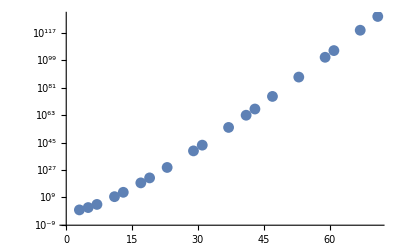

```mathematica
numberofnpolysoverq[q_,n_]:=1/n Sum[MoebiusMu[n/d]*q^d,{d,Divisors[n]}]
numberofnpolysoverq[5,2]
numpolysoverq[q_]:=Sum[1/n Sum[MoebiusMu[n/d]*q^d,{d,Divisors[n]}],{n,1,q-1}]
ListLogPlot[Table[{Prime[i],numpolysoverq[Prime[i]]},{i,2,30}]]
```